```mathematica
Odes={
s'[t]==-v1,
e'[t]==-v1+v3,
es'[t]==v1-v2,
ep'[t]==v2-v3,
p'[t]==v3};
RateEqs={
v1->k1f*e[t]*s[t]-k1b*es[t],
v2->k2f*es[t]-k2b*ep[t],
v3->k3f*ep[t]-k3b*e[t]*p[t]};
Parm={
k1f->100,k1b->10,
k2f->100,k2b->10,
k3f->100,k3b->10};
Init={
s[0]==1000,
e[0]==10,
es[0]==0,
ep[0]==0,
p[0]==0};
Vars={s,e,es,ep,p};
```

```mathematica
TimeSol=NDSolve[Join[Odes/.RateEqs/.Parm,Init],Vars,{t,0,100}];
```

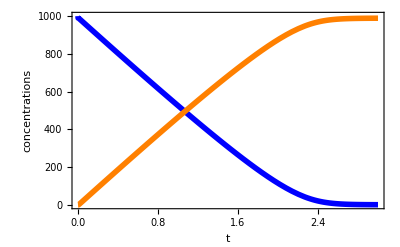

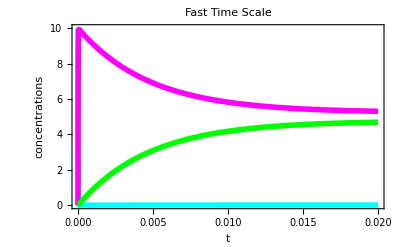

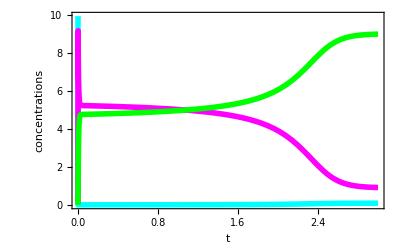

```mathematica
Plsp=Plot[Evaluate[{s[t],p[t]}/.TimeSol],{t,0,3},Frame->True,FrameLabel->{"t","concentrations"},BaseStyle->14,PlotStyle->{{Blue,Thickness[0.01]},{Orange,Thickness[0.01]}}]
Plot[Evaluate[{e[t],es[t],ep[t]}/.TimeSol],{t,0,0.02},Frame->True,FrameLabel->{"t","concentrations"},BaseStyle->14,PlotStyle->{{Cyan,Thickness[0.01]},{Magenta,Thickness[0.01]},{Green,Thickness[0.01]}},PlotLabel->"Fast Time Scale"]
Pleesep=Plot[Evaluate[{e[t],es[t],ep[t]}/.TimeSol],{t,0,3},Frame->True,FrameLabel->{"t","concentrations"},BaseStyle->14,PlotStyle->{{Cyan,Thickness[0.01]},{Magenta,Thickness[0.01]},{Green,Thickness[0.01]}}]
```

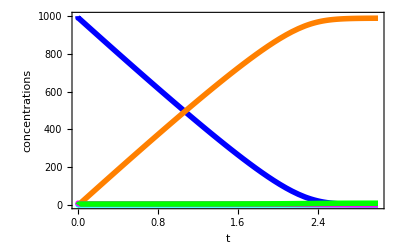

```mathematica
Show[Plsp,Pleesep]
```

Derivation of the quasi-state steady enzyme rate equation, the reversible Michaelis Menten equation

```mathematica
QSSSol=Solve[{v1-v2==0,v2-v3==0,eT==e[t]+es[t]+ep[t]}/.RateEqs,{e[t],es[t],ep[t]}][[1]]
```

{e[t]→-(-eT k1b k2b-eT k1b k3f-eT k2f k3f)/(k1b k2b+k1b k3f+k2f k3f+k1b k3b p[t]+k2b k3b p[t]+k2f k3b p[t]+k1f k2b s[t]+k1f k2f s[t]+k1f k3f s[t]),es[t]→-(-eT k2b k3b p[t]-eT k1f k2b s[t]-eT k1f k3f s[t])/(k1b k2b+k1b k3f+k2f k3f+k1b k3b p[t]+k2b k3b p[t]+k2f k3b p[t]+k1f k2b s[t]+k1f k2f s[t]+k1f k3f s[t]),ep[t]→-(-eT k1b k3b p[t]-eT k2f k3b p[t]-eT k1f k2f s[t])/(k1b k2b+k1b k3f+k2f k3f+k1b k3b p[t]+k2b k3b p[t]+k2f k3b p[t]+k1f k2b s[t]+k1f k2f s[t]+k1f k3f s[t])}

The following equation is on page 14 in the syllabus (immediately above Eq 4)

```mathematica
MMQSS=v3/.RateEqs/.QSSSol//FullSimplify
```

(-eT k1b k2b k3b p[t]+eT k1f k2f k3f s[t])/(k1b k2b+(k1b+k2f) k3f+(k1b+k2b+k2f) k3b p[t]+k1f (k2b+k2f+k3f) s[t])

```mathematica
QSSParm={Vmaxf->(eT k1f k2f k3f)/(k1f (k2b+k2f+k3f)),Vmaxb->(eT k1b k2b k3b)/((k1b+k2b+k2f) k3b),Kms->(k1b k2b+(k1b+k2f) k3f)/(k1f (k2b+k2f+k3f)),Kmp->(k1b k2b+(k1b+k2f) k3f)/((k1b+k2b+k2f) k3b)};
```

```mathematica
MMQSSsimple=(Vmaxf*s[t]/Kms-Vmaxb*p[t]/Kmp)/(1+s[t]/Kms+p[t]/Kmp);
```

```mathematica
QSSOde={
s'[t]==-v,
p'[t]==v}/.v->MMQSSsimple/.QSSParm/.Parm/.eT->10;
QSSInit={s[0]==1000,p[0]==0};
QSSVars={s,p};
QSSTimeSol=NDSolve[Join[QSSOde,QSSInit],QSSVars,{t,0,10}];
```

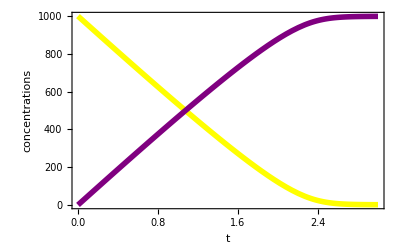

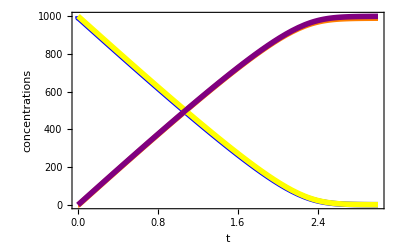

```mathematica
QSSPlsp=Plot[Evaluate[{s[t],p[t]}/.QSSTimeSol],{t,0,3},Frame->True,FrameLabel->{"t","concentrations"},BaseStyle->14,PlotStyle->{{Yellow,Thickness[0.01]},{Purple,Thickness[0.01]}}]
Show[Plsp,QSSPlsp]
```

To determine when the system reaches thermodynamic equilibrium we plot the rate as function of time

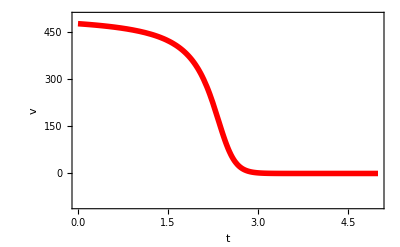

```mathematica
Plot[Evaluate[MMQSSsimple/.QSSParm/.Parm/.eT->10/.QSSTimeSol],{t,0,5},PlotRange->{-100,500},Frame->True,FrameLabel->{"t","v"},BaseStyle->14,PlotStyle->{{Red,Thickness[0.01]}}]
```

This means that t=5 the system has reached thermodynamic equilibrium.  Then the ratio of the concentrations of the product and the substrate are given by the Haldane relationship.  Let's check whether this equation is indeed valid.

The following ratio should equal
(Vmaxf*Kmp)/(Vmaxb*Kms)

```mathematica
Evaluate[p[t]/s[t]/.t->5/.QSSTimeSol]
```

{1000.}

```mathematica
(Vmaxf*Kmp)/(Vmaxb*Kms)/.QSSParm
%/.Parm
```

(k1f k2f k3f)/(k1b k2b k3b)

1000

And it does :)